```mathematica
ClearAll["Global`*"]
NotebookSave[]
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Function_Garch.m"];
```

```mathematica
nums=Volatility["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\goog.csv",90,5]
```

{0.00208028,1026.,0.696786,0.0000300146,0.}

Distribution Parameters

```mathematica
rm=0.06;
rs=0.001;
sigmam=nums[[1]];
sigmas=0.01;
S0m=nums[[2]];
S0s=sigmam;
a=nums[[3]];
b=nums[[4]];
w=nums[[5]];
```

Set Parameters

```mathematica
Num=500;
M=25000;
callput="Put";
n=50.;
T=1.;
k=40.;
```

```mathematica
distrib={NormalDistribution[rm,rs],NormalDistribution[sigmam,sigmas],NormalDistribution[S0m,S0s]};
```

```mathematica
matrix=Table[distrib,{i,1,Num}];
```

```mathematica
MatRand1=Map[RandomVariate,matrix,{2}];
MatRand2=Map[RandomVariate,matrix,{2}];
```

```mathematica
(*Simul[M,callput,n,T,K,r,sigma,S0]*)
```

```mathematica
(*Param=Table[{M,callput,If[Mod[i-1,Num*3]≥Num*2,nm+ns,If[Mod[i-1,Num*3]≥Num,nm,nm-ns]],If[Mod[i-1,Num*9]≥Num*6,Tm+Ts,If[Mod[i-1,Num*9]≥Num*3,Tm,Tm-Ts]],
If[Mod[i-1,Num*27]≥Num*18,Km+Ks,If[Mod[i-1,Num*27]≥Num*9,Km,Km-Ks]]},{i,1,Num*27}];*)
```

```mathematica
Param=Table[{M,callput,n,T,k,a,b,w},{i,1,Num}];(*non-random parameters*)
```

```mathematica
MatA=Join[Param,MatRand1,2];
MatB=Join[Param,MatRand2,2];
```

```mathematica
For[i=Dimensions[Param][[2]]+1;VMat={},i≤Dimensions[MatA][[2]],i++,tmp=MatB;tmp[[All,i]]=MatA[[All,i]];AppendTo[VMat,tmp]]
```

```mathematica
DateList[]
```

{2017,11,15,23,3,16.137964}

```mathematica
fA=ParallelTable[Simul@@MatA[[it3]],{it3,1,Num}];//AbsoluteTiming
```

Max::nord: Invalid comparison with -1031.71-10.2591 ⅈ attempted.

Max::nord: Invalid comparison with -993.591+82.8315 ⅈ attempted.

Max::nord: Invalid comparison with -1071.35+4.6707 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -1081.05+60.2548 ⅈ attempted.

Max::nord: Invalid comparison with -1006.97-62.2554 ⅈ attempted.

Max::nord: Invalid comparison with -1033.42+80.9902 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

$Aborted

```mathematica
DateList[]
```

{2017,11,15,22,37,10.465759}

```mathematica
fB=ParallelTable[Simul@@MatB[[it4]],{it4,1,Num}];//AbsoluteTiming
```

{0.236691,Null}

```mathematica
DateList[]
```

{2017,11,15,22,37,10.715434}

```mathematica
Monitor[For[it2=1;fVA={},it2<=Dimensions[VMat][[1]],it2++,tmp=ParallelTable[Simul@@VMat[[it2,it1]],{it1,1,Num}];AppendTo[fVA,tmp]],ProgressIndicator[it2,{1,Dimensions[VMat][[1]]}]];//AbsoluteTiming
```

{0.700707,Null}

```mathematica
DateList[]
```

{2017,11,15,22,37,11.463434}

```mathematica
(*For[x=1;Var={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fB[[w]]*(fVA[[x,w]]-fA[[w]]),{w,1,Num}];AppendTo[Var,tmp]]*)
```

```mathematica
For[x=1;Var1={},x≤Dimensions[fVA][[1]],x++,tmp=(1/Num*Sum[fA[[i]]*fVA[[x,i]],{i,Num}]-(1/Num*Sum[fA[[i]],{i,Num}])^2)/(1/Num*Sum[fA[[i]]*fA[[i]],{i,Num}]-(1/Num*Sum[fA[[i]],{i,Num}])^2);AppendTo[Var1,tmp]]
```

```mathematica
Var1
```

{0.492784,0.676184,0.643844}

```mathematica
For[x=1;Var2={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Var2,tmp]]
```

```mathematica
Var2/Total[Var2,2]
```

{0.15654,0.447372,0.396088}

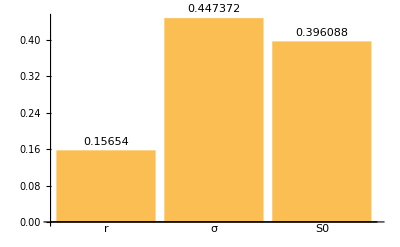

```mathematica
BarChart[Var2/Total[Var2,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

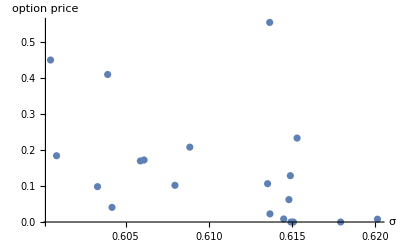

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

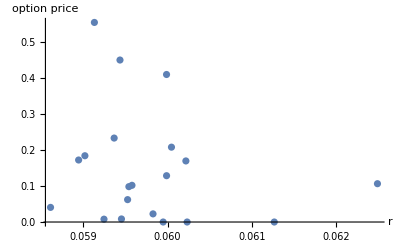

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

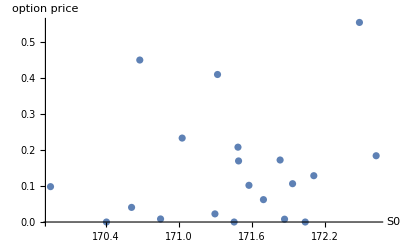

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA2.m",MatA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB2.m",MatB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA2.m",fA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB2.m",fB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA2.m",fVA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param2.m",Param[[1]]];
```

```mathematica
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\sigma2.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\r2.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\S02.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}],"eps"];
```

```mathematica
NotebookSave[]
```